```mathematica
Clear[d2,aa,ab,da]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
sq[n_, m_] := Floor[ n^m ]-Floor[(n-1)^m]
d2[n_, m_, k_]:=d2[n,m,k]= Sum[ sq[j,m]d2[Floor[n/j],m,k-1],{j,2,n}]
d2[n_,m_,0] := UnitStep[n-1]
dz[n_, m_,z_] := Sum[bin[z,k]d2[n,m,k],{k,0,Log2@n}]
ddz[n_,m_,z_] := dz[n,m,z]-dz[n-1,m,z]
aa[n_, m_] := aa[n,m]=ddz[n,1/m,MoebiusMu[m] /m]
ab[n_] := ab[n]=Sum[ aa[a1,1] aa[a2,2] aa[a3,3] aa[a5,5] aa[a6,6],{a1,1,n},{a2,1,n/a1},{a3,1,n/(a1 a2)},{a5,1,n/(a1 a2 a3)},{a6,1,n/(a1 a2 a3 a5)}]
ax[n_] := ab[n]-ab[n-1]
da[n_,k_] := da[n,k]=Sum[ ax[j] da[Floor[n/j],k-1],{j,2,n}]
da[n_, 0] := UnitStep[n-1]
ld[n_] := Sum[ (-1)^(k+1)/k da[n,k],{k,1,Log2@n}]
```

```mathematica
Expand@ddz[8,1/3,-1/3]
```

-1/3

```mathematica
Table[ax[n],{n,1,100}]
```

{1,1,1,1/2,1,1,1,1/6,1/2,1,1,1/2,1,1,1,1/24,1,1/2,1,1/2,1,1,1,1/6,1/2,1,1/6,1/2,1,1,1,1/120,1,1,1,1/4,1,1,1,1/6,1,1,1,1/2,1/2,1,1,1/24,1/2,1/2,1,1/2,1,1/6,1,1/6,1,1,1,1/2,1,1,1/2,1/720,1,1,1,1/2,1,1,1,1/12,1,1,1/2,1/2,1,1,1,1/24,1/24,1,1,1/2,1,1,1,1/6,1,1/2,1,1/2,1,1,1,1/120,1,1/2,1/2,1/4}

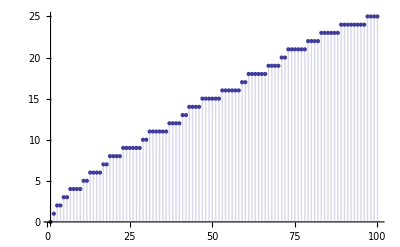

```mathematica
DiscretePlot[ ld[n],{n,1,100}]
```